```mathematica
(*R is the radius, interval is [-R,R]*)
startR=0;
endR=5
(*intervals*)
M=1000;
(*sites is intervals + 1*)
sites=M+1;
ϵ=1;
a=1;
(*define m_k (the factor in each element of the matrix*)
mk[j_]=((startR+Δx*j)^3-(startR+Δx*j-Δx)^3)/(3 Δx^2);
(*electron density function*)
ρ[r_]=If[r>=0,(1/(π a^3)ⅇ^(-2 r/a)),(1/(π a^3)ⅇ^(2 r/a))];
(*integrals that come from integrating the electron density and everything*)
int[R_,v_,a1_,a2_]:=NIntegrate[1/ϵ r^2 ρ[r]*v,{r,a1,a2}];
(*interval length*)
Δx=(endR-startR)/M;
(*defines elements*)
linFunc[a_,r_]:=If[r<a,1/Δx(r-a)+1,-1/Δx(r-a)+1];
RealFunction[r_]=If[r>0,1/(4π ϵ a^2)(a^2/r-(a^2/r-a)ⅇ^(-2 r/a)),1/(4π ϵ a^2)(-a^2/r-(-a^2/r-a)ⅇ^(2 r/a))];
boundary[r_]:=If[0≤r<endR/2,Limit[RealFunction[x],x->0],1/(4 π ϵ)1/Abs[r]]
```

5

```mathematica
(*Making a table of elements in the vector on the RHS*)
RHS=Table[int[R,linFunc[i,r],i-Δx,i+Δx],{i,startR+Δx,endR-Δx,Δx}];
```

```mathematica
(*check dimensions*)
b=RHS;
b[[1]]=b[[1]]+mk[1]*boundary[startR]
b[[Length[b]]]=b[[Length[b]]]+mk[sites]*boundary[endR]
Dimensions[b]
(*Remove the first 2 rows and last 2 rows because of boundary conditions?*)
(*check dimen
sions*)
```

0.000397902

79.6571

{999}

```mathematica
boundary[0]
```

3/(4 π)

```mathematica
Limit[RealFunction[r],r->0]
```

3/(4 π)

```mathematica
(*define array of zeroes*)
LHS=ConstantArray[0,{sites,sites}];
(*create a loop to fill in elements*)
For[i=0,i<sites,i++,
If[i+1<=sites&&i>0,LHS[[i+1,i]]=-mk[i]];
If[i+1<=sites&&i>=0,LHS[[i+1,i+1]]=mk[i+1]+mk[i]];
If[i+2<=sites,LHS[[i+1, i+2]]=-mk[i+1]];
]
```

```mathematica
LHS//MatrixForm;
```

```mathematica
(*check dimensions*)
Dimensions[LHS]
```

{1001,1001}

```mathematica
(*check dimensions*)
Dimensions[b]
```

{999}

```mathematica
LHS=Delete[LHS,{{1},{sites}}];
(*delete the first and last columns in the matrix*)
LHS=Drop[LHS,None,{1,1}];
LHS=Drop[LHS,None,{sites-1,sites-1}];
```

```mathematica
Dimensions[LHS]
```

{999,999}

```mathematica
(*solve the system*)
system=LinearSolve[LHS,b];
```

```mathematica
listOfR=Table[startR+Δx*j,{j,1,M-1} ];
```

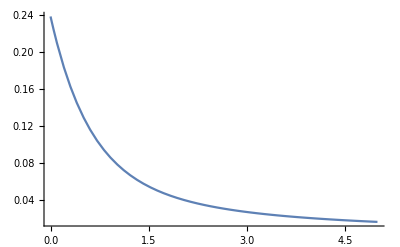

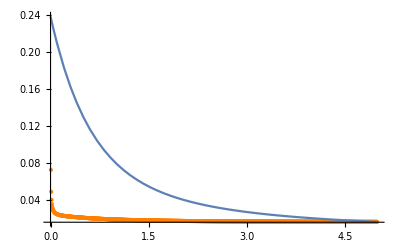

```mathematica
temp1=ListPlot[Transpose[{listOfR,system}],PlotStyle->{Orange}];
temp2=Plot[If[r>0,1/(4π ϵ a^2)(a^2/r-(a^2/r-a)ⅇ^(-2 r/a)),1/(4π ϵ a^2)(-a^2/r-(-a^2/r-a)ⅇ^(2 r/a))],{r,startR,endR},PlotRange->All]
Show[temp1,temp2,PlotRange->All]
```

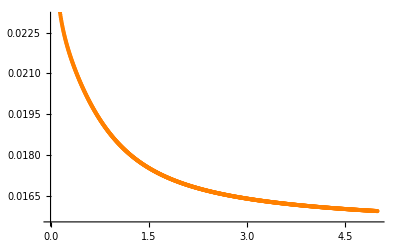

```mathematica
temp1
```

```mathematica
system[[1]]
```

0.0723767

```mathematica
N[boundary[-R]]
```

If[0.≤-1. R<2.5,lim_(x→0.) RealFunction[x],((1. 0.0795775) 1.)/(1. Abs[R])]

```mathematica
system[[Length[system]]]
```

0.015948

```mathematica
RHS
```

{1.44012×10^-8,5.05418×10^-8,1.09101×10^-7,1.88706×10^-7,2.88035×10^-7,4.05824×10^-7,5.40856×10^-7,6.91968×10^-7,8.58042×10^-7,1.03801×10^-6,1.23084×10^-6,1.43555×10^-6,1.6512×10^-6,1.8769×10^-6,2.11177×10^-6,2.35501×10^-6,2.60581×10^-6,2.86343×10^-6,3.12715×10^-6,3.39628×10^-6,3.67017×10^-6,3.94819×10^-6,4.22976×10^-6,4.51431×10^-6,4.80129×10^-6,5.09019×10^-6,5.38053×10^-6,5.67185×10^-6,5.96371×10^-6,6.25568×10^-6,6.54738×10^-6,6.83843×10^-6,7.12848×10^-6,7.4172×10^-6,7.70426×10^-6,7.98938×10^-6,8.27227×10^-6,8.55268×10^-6,8.83034×10^-6,9.10504×10^-6,9.37656×10^-6,9.64469×10^-6,9.90924×10^-6,0.00001017,0.0000104269,0.0000106797,0.0000109284,0.0000111726,0.0000114125,0.0000116477,0.0000118783,0.0000121042,0.0000123252,0.0000125414,0.0000127526,0.0000129587,0.0000131598,0.0000133558,0.0000135467,0.0000137324,0.0000139129,0.0000140882,0.0000142583,0.0000144232,0.0000145828,0.0000147373,0.0000148865,0.0000150306,0.0000151694,0.0000153032,0.0000154318,0.0000155553,0.0000156738,0.0000157872,0.0000158957,0.0000159992,0.0000160978,0.0000161916,0.0000162805,0.0000163647,0.0000164442,0.000016519,0.0000165893,0.000016655,0.0000167162,0.000016773,0.0000168255,0.0000168736,0.0000169175,0.0000169573,0.0000169929,0.0000170245,0.0000170522,0.0000170759,0.0000170958,0.0000171119,0.0000171244,0.0000171332,0.0000171384,0.0000171401,0.0000171384,0.0000171334,0.000017125,0.0000171135,0.0000170987,0.0000170809,0.0000170601,0.0000170363,0.0000170096,0.0000169802,0.0000169479,0.000016913,0.0000168755,0.0000168354,0.0000167928,0.0000167478,0.0000167004,0.0000166508,0.0000165989,0.0000165448,0.0000164886,0.0000164304,0.0000163701,0.0000163079,0.0000162439,0.000016178,0.0000161104,0.000016041,0.0000159701,0.0000158975,0.0000158233,0.0000157477,0.0000156707,0.0000155922,0.0000155124,0.0000154314,0.0000153491,0.0000152656,0.0000151809,0.0000150952,0.0000150084,0.0000149207,0.0000148319,0.0000147423,0.0000146518,0.0000145604,0.0000144683,0.0000143754,0.0000142818,0.0000141876,0.0000140927,0.0000139972,0.0000139011,0.0000138046,0.0000137075,0.00001361,0.0000135121,0.0000134138,0.0000133152,0.0000132162,0.000013117,0.0000130174,0.0000129177,0.0000128177,0.0000127176,0.0000126174,0.000012517,0.0000124165,0.000012316,0.0000122154,0.0000121148,0.0000120142,0.0000119136,0.0000118131,0.0000117127,0.0000116123,0.0000115121,0.000011412,0.0000113121,0.0000112123,0.0000111128,0.0000110134,0.0000109143,0.0000108154,0.0000107168,0.0000106185,0.0000105204,0.0000104227,0.0000103253,0.0000102282,0.0000101315,0.0000100351,9.93916×10^-6,9.84357×10^-6,9.74838×10^-6,9.65361×10^-6,9.55926×10^-6,9.46534×10^-6,9.37187×10^-6,9.27885×10^-6,9.1863×10^-6,9.09421×10^-6,9.00262×10^-6,8.91151×10^-6,8.8209×10^-6,8.73079×10^-6,8.6412×10^-6,8.55213×10^-6,8.46358×10^-6,8.37557×10^-6,8.2881×10^-6,8.20117×10^-6,8.11479×10^-6,8.02897×10^-6,7.94371×10^-6,7.85902×10^-6,7.77489×10^-6,7.69134×10^-6,7.60837×10^-6,7.52597×10^-6,7.44417×10^-6,7.36295×10^-6,7.28232×10^-6,7.20228×10^-6,7.12284×10^-6,7.044×10^-6,6.96575×10^-6,6.88811×10^-6,6.81108×10^-6,6.73464×10^-6,6.65882×10^-6,6.5836×10^-6,6.50898×10^-6,6.43498×10^-6,6.36159×10^-6,6.2888×10^-6,6.21662×10^-6,6.14506×10^-6,6.0741×10^-6,6.00375×10^-6,5.93402×10^-6,5.86488×10^-6,5.79636×10^-6,5.72844×10^-6,5.66113×10^-6,5.59443×10^-6,5.52832×10^-6,5.46282×10^-6,5.39792×10^-6,5.33362×10^-6,5.26991×10^-6,5.2068×10^-6,5.14429×10^-6,5.08237×10^-6,5.02103×10^-6,4.96029×10^-6,4.90013×10^-6,4.84055×10^-6,4.78155×10^-6,4.72313×10^-6,4.66529×10^-6,4.60802×10^-6,4.55132×10^-6,4.49519×10^-6,4.43962×10^-6,4.38462×10^-6,4.33017×10^-6,4.27628×10^-6,4.22294×10^-6,4.17016×10^-6,4.11792×10^-6,4.06622×10^-6,4.01506×10^-6,3.96445×10^-6,3.91436×10^-6,3.86481×10^-6,3.81578×10^-6,3.76728×10^-6,3.71929×10^-6,3.67183×10^-6,3.62487×10^-6,3.57843×10^-6,3.53249×10^-6,3.48706×10^-6,3.44213×10^-6,3.39769×10^-6,3.35374×10^-6,3.31028×10^-6,3.2673×10^-6,3.22481×10^-6,3.18279×10^-6,3.14124×10^-6,3.10017×10^-6,3.05956×10^-6,3.01941×10^-6,2.97972×10^-6,2.94049×10^-6,2.90171×10^-6,2.86337×10^-6,2.82548×10^-6,2.78802×10^-6,2.751×10^-6,2.71442×10^-6,2.67826×10^-6,2.64253×10^-6,2.60721×10^-6,2.57232×10^-6,2.53784×10^-6,2.50376×10^-6,2.4701×10^-6,2.43683×10^-6,2.40396×10^-6,2.37149×10^-6,2.33941×10^-6,2.30771×10^-6,2.2764×10^-6,2.24547×10^-6,2.21492×10^-6,2.18474×10^-6,2.15492×10^-6,2.12547×10^-6,2.09639×10^-6,2.06766×10^-6,2.03929×10^-6,2.01126×10^-6,1.98359×10^-6,1.95626×10^-6,1.92927×10^-6,1.90261×10^-6,1.87629×10^-6,1.8503×10^-6,1.82464×10^-6,1.7993×10^-6,1.77428×10^-6,1.74958×10^-6,1.72519×10^-6,1.70111×10^-6,1.67733×10^-6,1.65386×10^-6,1.63069×10^-6,1.60782×10^-6,1.58524×10^-6,1.56295×10^-6,1.54095×10^-6,1.51923×10^-6,1.49779×10^-6,1.47663×10^-6,1.45575×10^-6,1.43513×10^-6,1.41479×10^-6,1.39471×10^-6,1.37489×10^-6,1.35534×10^-6,1.33604×10^-6,1.31699×10^-6,1.2982×10^-6,1.27965×10^-6,1.26135×10^-6,1.24329×10^-6,1.22547×10^-6,1.20788×10^-6,1.19054×10^-6,1.17342×10^-6,1.15653×10^-6,1.13986×10^-6,1.12342×10^-6,1.1072×10^-6,1.0912×10^-6,1.07542×10^-6,1.05984×10^-6,1.04448×10^-6,1.02932×10^-6,1.01437×10^-6,9.99627×10^-7,9.8508×10^-7,9.70731×10^-7,9.56577×10^-7,9.42616×10^-7,9.28846×10^-7,9.15265×10^-7,9.01869×10^-7,8.88658×10^-7,8.75628×10^-7,8.62777×10^-7,8.50103×10^-7,8.37604×10^-7,8.25278×10^-7,8.13123×10^-7,8.01135×10^-7,7.89314×10^-7,7.77658×10^-7,7.66163×10^-7,7.54829×10^-7,7.43652×10^-7,7.32632×10^-7,7.21765×10^-7,7.11051×10^-7,7.00487×10^-7,6.90071×10^-7,6.79801×10^-7,6.69676×10^-7,6.59694×10^-7,6.49852×10^-7,6.40149×10^-7,6.30584×10^-7,6.21153×10^-7,6.11857×10^-7,6.02692×10^-7,5.93657×10^-7,5.84751×10^-7,5.75972×10^-7,5.67317×10^-7,5.58786×10^-7,5.50377×10^-7,5.42088×10^-7,5.33918×10^-7,5.25865×10^-7,5.17927×10^-7,5.10104×10^-7,5.02393×10^-7,4.94792×10^-7,4.87302×10^-7,4.79919×10^-7,4.72643×10^-7,4.65472×10^-7,4.58404×10^-7,4.51439×10^-7,4.44575×10^-7,4.37811×10^-7,4.31144×10^-7,4.24575×10^-7,4.18101×10^-7,4.11722×10^-7,4.05436×10^-7,3.99241×10^-7,3.93137×10^-7,3.87122×10^-7,3.81195×10^-7,3.75355×10^-7,3.696×10^-7,3.6393×10^-7,3.58344×10^-7,3.52839×10^-7,3.47416×10^-7,3.42072×10^-7,3.36807×10^-7,3.3162×10^-7,3.2651×10^-7,3.21475×10^-7,3.16514×10^-7,3.11627×10^-7,3.06813×10^-7,3.0207×10^-7,2.97397×10^-7,2.92794×10^-7,2.88259×10^-7,2.83792×10^-7,2.79391×10^-7,2.75056×10^-7,2.70785×10^-7,2.66579×10^-7,2.62435×10^-7,2.58353×10^-7,2.54333×10^-7,2.50372×10^-7,2.46471×10^-7,2.42629×10^-7,2.38844×10^-7,2.35116×10^-7,2.31444×10^-7,2.27828×10^-7,2.24266×10^-7,2.20757×10^-7,2.17302×10^-7,2.13899×10^-7,2.10547×10^-7,2.07246×10^-7,2.03995×10^-7,2.00793×10^-7,1.9764×10^-7,1.94534×10^-7,1.91476×10^-7,1.88464×10^-7,1.85498×10^-7,1.82577×10^-7,1.797×10^-7,1.76868×10^-7,1.74078×10^-7,1.71331×10^-7,1.68626×10^-7,1.65963×10^-7,1.6334×10^-7,1.60757×10^-7,1.58214×10^-7,1.55709×10^-7,1.53243×10^-7,1.50815×10^-7,1.48424×10^-7,1.4607×10^-7,1.43752×10^-7,1.4147×10^-7,1.39223×10^-7,1.3701×10^-7,1.34832×10^-7,1.32687×10^-7,1.30575×10^-7,1.28496×10^-7,1.26449×10^-7,1.24433×10^-7,1.22449×10^-7,1.20496×10^-7,1.18572×10^-7,1.16679×10^-7,1.14815×10^-7,1.1298×10^-7,1.11173×10^-7,1.09395×10^-7,1.07644×10^-7,1.0592×10^-7,1.04223×10^-7,1.02553×10^-7,1.00908×10^-7,9.92893×10^-8,9.76958×10^-8,9.61271×10^-8,9.4583×10^-8,9.3063×10^-8,9.15667×10^-8,9.00939×10^-8,8.86441×10^-8,8.7217×10^-8,8.58123×10^-8,8.44296×10^-8,8.30686×10^-8,8.1729×10^-8,8.04104×10^-8,7.91126×10^-8,7.78351×10^-8,7.65778×10^-8,7.53402×10^-8,7.41221×10^-8,7.29233×10^-8,7.17433×10^-8,7.05819×10^-8,6.94389×10^-8,6.83139×10^-8,6.72067×10^-8,6.6117×10^-8,6.50446×10^-8,6.39891×10^-8,6.29503×10^-8,6.1928×10^-8,6.09218×10^-8,5.99317×10^-8,5.89572×10^-8,5.79982×10^-8,5.70545×10^-8,5.61257×10^-8,5.52117×10^-8,5.43122×10^-8,5.34271×10^-8,5.2556×10^-8,5.16988×10^-8,5.08553×10^-8,5.00252×10^-8,4.92084×10^-8,4.84046×10^-8,4.76136×10^-8,4.68353×10^-8,4.60694×10^-8,4.53157×10^-8,4.45742×10^-8,4.38444×10^-8,4.31264×10^-8,4.24198×10^-8,4.17246×10^-8,4.10406×10^-8,4.03675×10^-8,3.97052×10^-8,3.90535×10^-8,3.84123×10^-8,3.77814×10^-8,3.71607×10^-8,3.65499×10^-8,3.5949×10^-8,3.53577×10^-8,3.4776×10^-8,3.42036×10^-8,3.36404×10^-8,3.30864×10^-8,3.25413×10^-8,3.20049×10^-8,3.14773×10^-8,3.09581×10^-8,3.04474×10^-8,2.99449×10^-8,2.94505×10^-8,2.89641×10^-8,2.84856×10^-8,2.80149×10^-8,2.75518×10^-8,2.70961×10^-8,2.66479×10^-8,2.6207×10^-8,2.57732×10^-8,2.53464×10^-8,2.49266×10^-8,2.45136×10^-8,2.41073×10^-8,2.37076×10^-8,2.33144×10^-8,2.29276×10^-8,2.25471×10^-8,2.21728×10^-8,2.18046×10^-8,2.14424×10^-8,2.10861×10^-8,2.07356×10^-8,2.03909×10^-8,2.00517×10^-8,1.97181×10^-8,1.939×10^-8,1.90672×10^-8,1.87497×10^-8,1.84374×10^-8,1.81302×10^-8,1.7828×10^-8,1.75308×10^-8,1.72384×10^-8,1.69508×10^-8,1.6668×10^-8,1.63897×10^-8,1.61161×10^-8,1.58469×10^-8,1.55822×10^-8,1.53218×10^-8,1.50656×10^-8,1.48137×10^-8,1.45659×10^-8,1.43222×10^-8,1.40825×10^-8,1.38468×10^-8,1.36149×10^-8,1.33869×10^-8,1.31626×10^-8,1.2942×10^-8,1.2725×10^-8,1.25116×10^-8,1.23018×10^-8,1.20954×10^-8,1.18924×10^-8,1.16927×10^-8,1.14964×10^-8,1.13033×10^-8,1.11134×10^-8,1.09266×10^-8,1.07429×10^-8,1.05623×10^-8,1.03846×10^-8,1.02099×10^-8,1.00381×10^-8,9.8691×10^-9,9.70293×10^-9,9.53951×10^-9,9.3788×10^-9,9.22076×10^-9,9.06533×10^-9,8.91249×10^-9,8.76219×10^-9,8.61438×10^-9,8.46903×10^-9,8.32609×10^-9,8.18553×10^-9,8.04731×10^-9,7.91139×10^-9,7.77773×10^-9,7.64629×10^-9,7.51704×10^-9,7.38994×10^-9,7.26496×10^-9,7.14207×10^-9,7.02122×10^-9,6.90239×10^-9,6.78554×10^-9,6.67064×10^-9,6.55766×10^-9,6.44656×10^-9,6.33732×10^-9,6.2299×10^-9,6.12428×10^-9,6.02042×10^-9,5.9183×10^-9,5.81789×10^-9,5.71916×10^-9,5.62208×10^-9,5.52663×10^-9,5.43277×10^-9,5.34048×10^-9,5.24975×10^-9,5.16053×10^-9,5.0728×10^-9,4.98655×10^-9,4.90175×10^-9,4.81837×10^-9,4.73638×10^-9,4.65578×10^-9,4.57652×10^-9,4.4986×10^-9,4.42199×10^-9,4.34666×10^-9,4.2726×10^-9,4.19979×10^-9,4.1282×10^-9,4.05781×10^-9,3.98861×10^-9,3.92058×10^-9,3.85369×10^-9,3.78792×10^-9,3.72327×10^-9,3.6597×10^-9,3.5972×10^-9,3.53576×10^-9,3.47536×10^-9,3.41597×10^-9,3.35758×10^-9,3.30018×10^-9,3.24375×10^-9,3.18828×10^-9,3.13374×10^-9,3.08012×10^-9,3.0274×10^-9,2.97558×10^-9,2.92464×10^-9,2.87455×10^-9,2.82531×10^-9,2.77691×10^-9,2.72933×10^-9,2.68255×10^-9,2.63656×10^-9,2.59135×10^-9,2.54691×10^-9,2.50322×10^-9,2.46027×10^-9,2.41805×10^-9,2.37654×10^-9,2.33574×10^-9,2.29563×10^-9,2.25621×10^-9,2.21745×10^-9,2.17935×10^-9,2.14189×10^-9,2.10508×10^-9,2.06888×10^-9,2.03331×10^-9,1.99833×10^-9,1.96396×10^-9,1.93016×10^-9,1.89695×10^-9,1.86429×10^-9,1.8322×10^-9,1.80065×10^-9,1.76963×10^-9,1.73915×10^-9,1.70918×10^-9,1.67973×10^-9,1.65077×10^-9,1.62231×10^-9,1.59434×10^-9,1.56684×10^-9,1.53981×10^-9,1.51324×10^-9,1.48713×10^-9,1.46146×10^-9,1.43623×10^-9,1.41143×10^-9,1.38706×10^-9,1.3631×10^-9,1.33955×10^-9,1.3164×10^-9,1.29365×10^-9,1.27129×10^-9,1.24931×10^-9,1.2277×10^-9,1.20647×10^-9,1.1856×10^-9,1.16508×10^-9,1.14492×10^-9,1.1251×10^-9,1.10563×10^-9,1.08648×10^-9,1.06767×10^-9,1.04917×10^-9,1.031×10^-9,1.01313×10^-9,9.95573×10^-10,9.78316×10^-10,9.61355×10^-10,9.44685×10^-10,9.28301×10^-10,9.12199×10^-10,8.96373×10^-10,8.80819×10^-10,8.65532×10^-10,8.50507×10^-10,8.35741×10^-10,8.21229×10^-10,8.06966×10^-10,7.92949×10^-10,7.79172×10^-10,7.65633×10^-10,7.52327×10^-10,7.39249×10^-10,7.26397×10^-10,7.13766×10^-10,7.01353×10^-10,6.89153×10^-10,6.77164×10^-10,6.65381×10^-10,6.53801×10^-10,6.42421×10^-10,6.31237×10^-10,6.20246×10^-10,6.09444×10^-10,5.98829×10^-10,5.88397×10^-10,5.78145×10^-10,5.6807×10^-10,5.58169×10^-10,5.48438×10^-10,5.38876×10^-10,5.29479×10^-10,5.20245×10^-10,5.1117×10^-10,5.02252×10^-10,4.93488×10^-10,4.84875×10^-10,4.76412×10^-10,4.68095×10^-10,4.59922×10^-10,4.5189×10^-10,4.43997×10^-10,4.36241×10^-10,4.28619×10^-10,4.21129×10^-10,4.13769×10^-10,4.06536×10^-10,3.99429×10^-10,3.92445×10^-10,3.85582×10^-10,3.78838×10^-10,3.7221×10^-10,3.65698×10^-10,3.59299×10^-10,3.5301×10^-10,3.46831×10^-10,3.40759×10^-10,3.34792×10^-10,3.28929×10^-10,3.23168×10^-10,3.17507×10^-10,3.11944×10^-10,3.06478×10^-10,3.01107×10^-10,2.95829×10^-10,2.90643×10^-10,2.85547×10^-10,2.80539×10^-10,2.75619×10^-10,2.70784×10^-10,2.66033×10^-10,2.61365×10^-10,2.56779×10^-10,2.52272×10^-10,2.47843×10^-10,2.43492×10^-10,2.39216×10^-10,2.35015×10^-10,2.30887×10^-10,2.26831×10^-10,2.22846×10^-10,2.1893×10^-10,2.15082×10^-10,2.11301×10^-10,2.07587×10^-10,2.03937×10^-10,2.00351×10^-10,1.96827×10^-10,1.93365×10^-10,1.89963×10^-10,1.86621×10^-10,1.83337×10^-10,1.8011×10^-10,1.7694×10^-10,1.73825×10^-10,1.70764×10^-10,1.67757×10^-10,1.64802×10^-10,1.61899×10^-10,1.59047×10^-10,1.56245×10^-10,1.53492×10^-10,1.50786×10^-10,1.48129×10^-10,1.45517×10^-10,1.42951×10^-10,1.40431×10^-10,1.37954×10^-10,1.35521×10^-10,1.3313×10^-10,1.30781×10^-10,1.28473×10^-10,1.26206×10^-10,1.23978×10^-10,1.2179×10^-10,1.1964×10^-10,1.17527×10^-10,1.15451×10^-10,1.13412×10^-10,1.11409×10^-10,1.09441×10^-10,1.07507×10^-10,1.05607×10^-10,1.03741×10^-10,1.01907×10^-10,1.00105×10^-10,9.83354×10^-11,9.65965×10^-11,9.48882×10^-11,9.32098×10^-11,9.15609×10^-11,8.9941×10^-11,8.83496×10^-11,8.67861×10^-11,8.525×10^-11,8.3741×10^-11,8.22585×10^-11,8.0802×10^-11,7.93712×10^-11,7.79655×10^-11,7.65846×10^-11,7.52279×10^-11,7.38951×10^-11,7.25857×10^-11,7.12994×10^-11,7.00357×10^-11,6.87943×10^-11,6.75747×10^-11,6.63766×10^-11,6.51996×10^-11,6.40433×10^-11,6.29074×10^-11,6.17915×10^-11,6.06953×10^-11,5.96183×10^-11,5.85604×10^-11,5.75211×10^-11,5.65001×10^-11,5.54971×10^-11,5.45118×10^-11,5.35439×10^-11,5.25931×10^-11,5.1659×10^-11,5.07414×10^-11,4.984×10^-11,4.89545×10^-11,4.80847×10^-11,4.72302×10^-11,4.63907×10^-11,4.55661×10^-11,4.47561×10^-11,4.39604×10^-11,4.31787×10^-11,4.24108×10^-11,4.16565×10^-11,4.09156×10^-11,4.01877×10^-11,3.94727×10^-11,3.87703×10^-11,3.80804×10^-11,3.74026×10^-11,3.67369×10^-11,3.60829×10^-11,3.54405×10^-11,3.48094×10^-11,3.41895×10^-11,3.35806×10^-11,3.29825×10^-11,3.23949×10^-11,3.18178×10^-11,3.12508×10^-11,3.06939×10^-11,3.01469×10^-11,2.96096×10^-11,2.90817×10^-11,2.85633×10^-11,2.8054×10^-11,2.75537×10^-11,2.70623×10^-11,2.65796×10^-11}

```mathematica
Cos[21 Degree]^2*Cos[42 Degree]^2
```

Cos[21 °]^2 Cos[42 °]^2

```mathematica
N[Cos[21 °]^2 Cos[42 °]^2]
```

0.481338

```mathematica
N[Cos[21 °]^2 Cos[42 °]^2]
```

0.481338

```mathematica
FullSimplify[1/r^2 D[r^2*D[1/(4π ϵ a^2)(a^2/r-(a^2/r-a)ⅇ^(-2 r/a)),{r}],r]]
```

(ⅇ^(-2 r) (-2+r))/(π r)

```mathematica
a=1
temp=NDSolve[{D[x^2 D[f[x],x],x]==-x^2 ρ[x],f[0.001]==3/(4 π),f[10]==1/(4 π)1/5},f, {x,0.001, 10}]
```

1

{{f→InterpolatingFunction[…]}}

{InterpolatingFunction[…][x]}

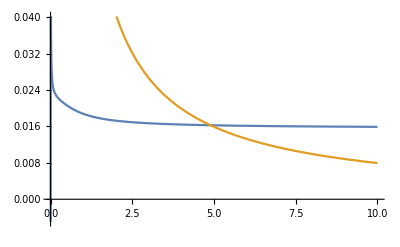

```mathematica
g[x_]=f[x]/.temp
Plot[{g[x],RealFunction[x]}, {x,0,10}]
```

```mathematica
N[1/(4 π)1/5]
```

0.0159155

```mathematica
Clear[a]
```

```mathematica
(1/(π a^3)ⅇ^(-2 r/a))^2
```

ⅇ^(-(4 r)/a)/(a^6 π^2)

```mathematica
FullSimplify[1/r^2 D[r^2 D[RealFunction[r],r]], Assumptions->r>0]
```

-(ⅇ^(-2 r) (-1+ⅇ^(2 r)+2 (-1+r) r))/(4 π r^2)

```mathematica
Integrate[1/ϵ r^2 ⅇ^(-(2 r)/a)/(π a^3)*linFunc[b, r],{r,b-δx,b+δx},Assumptions->{r>0,b-δx>0,δx>0}]
```

-1/(4 π)ⅇ^(-2 b-2 δx) (-299-398 b-198 b^2+600 ⅇ^(2 δx)+800 b ⅇ^(2 δx)+400 b^2 ⅇ^(2 δx)-301 ⅇ^(4 δx)-402 b ⅇ^(4 δx)-202 b^2 ⅇ^(4 δx)-598 δx-796 b δx-400 b^2 δx+602 ⅇ^(4 δx) δx+804 b ⅇ^(4 δx) δx+400 b^2 ⅇ^(4 δx) δx-598 δx^2-800 b δx^2-602 ⅇ^(4 δx) δx^2-800 b ⅇ^(4 δx) δx^2-400 δx^3+400 ⅇ^(4 δx) δx^3)